```mathematica
<<JLink`;
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx8192m"]



(*Import list of Gross Outputs for all Sectors*)
go2014=Import["Inflation/GO_2014.xlsx"][[1,1]];
```

LinkObject[…]

```mathematica
(*Import WIOD IO table for 2014 w/o labels. Transpose to enable easier division by columns*)
io2014=Transpose[Import["Inflation/IO_2014.xlsx"][[1]]];
```

```mathematica
(*Calculate technological coefficients by dividing each row (column of original IO table) by corresponding GO value. Transpose back.*)
techcoeff=Transpose[Quiet[Table[io2014[[k]]/go2014[[k]]/. Indeterminate:>0/. ComplexInfinity:>0,{k,1,Length[io2014]}]]];
```

```mathematica
(*Calculate Leontief inverse*)
leontiefinverse=Inverse[(IdentityMatrix[Length[techcoeff]]-techcoeff)];
```

```mathematica
Clear[aee,axe]
(*Define (transposed) A matrix with row and column for exogenous sector dropped*)
aee[k_]:=Transpose[Drop[leontiefinverse,{k},{k}]]
```

```mathematica
(*Take row of exogenous sector, drop own entry and transpose (which is not necessary for vectors in Mma and hence omitted)*)
axe[k_]:=Drop[techcoeff[[k]],{k}]
```

```mathematica
(*Import price time series (intermediate goods price levels, II_PI in WIOD SEA)*)
prices=Import["Inflation/iiprices_full.xlsx"][[1]];
(*Define price shocks as SD of log differences over all years*)
priceshocks=Table[StandardDeviation[Differences[Log[Drop[prices,1][[All,5;;-1]][[k]]]]],{k,1,Length[prices]-1}];
```

```mathematica
(*Import demand table for 2014*)
demand2014=Import["Inflation/demand2014.xlsx"][[1]];
```

```mathematica
(*Find position of HH demand*)
poshh=Flatten[Position[demand2014[[1]],"CONS_h"]];
```

```mathematica
(*Take HH demand*)
hhdemand1=Transpose[Drop[demand2014,2]][[poshh]];
```

```mathematica
(*Calculate HH demand on sectoral level over all countries and construct shares by dividing through total*)
hhdemand=Table[Total[Transpose[hhdemand1][[k]]],{k,1,Length[Transpose[hhdemand1]]}];
hhdemandshare=Flatten[{hhdemand[[1;;Length[priceshocks]]]/Total[hhdemand[[1;;Length[priceshocks]]]],ConstantArray[0,Length[leontiefinverse]-Length[priceshocks]]}];
```

```mathematica
(*Calculate indirect effect as in Weber et al.*)
indirect[k_]:=aee[k].axe[k].Drop[hhdemandshare,{k}]*priceshocks[[k]]
```

```mathematica
(*Calculate direct effect as in Weber et al.*)
direct[k_]:=hhdemandshare[[k]]*priceshocks[[k]]
```

```mathematica
(*Export results with country and sector labels, sort by indirect impact*)
Export["impacttable.xlsx",Reverse[SortBy[Table[{Drop[prices,1][[k,1]],Drop[prices,1][[k,4]],Drop[prices,1][[k,3]],direct[k],indirect[k],direct[k]+indirect[k]},{k,1,Length[priceshocks]}],Last]]]
```

impacttable.xlsx

```mathematica
(*Find position of HH demand*)
poshh=Flatten[Position[demand2014[[1]],"CONS_h"]];
labels=DeleteDuplicates[demand2014[[2]]];
eu28countries={"AUT","BEL","BGR","CZE","CYP","FIN","DEU","DNK","ESP","EST","FRA","GBR","GRC","HRV","HUN","IRL","ITA","LTU","LUX","LVA","MLT","NLD","POL","PRT","ROU","SVK","SVN","SWE"};

positionseu28=Flatten[Table[Position[labels,eu28countries[[k]]],{k,1,Length[eu28countries]}]];
```

```mathematica
(*Calculate for demand shares only within EU28 countries*)
(*Take HH demand EU28*)
hhdemandeu1=Transpose[Drop[demand2014,2]][[poshh]][[positionseu28]];
hhdemandeu=Table[Total[Transpose[hhdemandeu1][[k]]],{k,1,Length[Transpose[hhdemandeu1]]}];
```

```mathematica
hhdemandshareeu=Flatten[{hhdemandeu[[1;;Length[priceshocks]]]/Total[hhdemandeu[[1;;Length[priceshocks]]]],ConstantArray[0,Length[leontiefinverse]-Length[priceshocks]]}];
```

```mathematica
(*Calculate indirect effect as in Weber et al. for EU28 shares*)
indirecteu[k_]:=aee[k].axe[k].Drop[hhdemandshareeu,{k}]*priceshocks[[k]]
```

```mathematica
(*Calculate direct effect as in Weber et al.  for EU28 shares*)
directeu[k_]:=hhdemandshareeu[[k]]*priceshocks[[k]]
```

```mathematica
Export["impacttableeudemand.xlsx",Reverse[SortBy[Table[{Drop[prices,1][[k,1]],Drop[prices,1][[k,4]],Drop[prices,1][[k,3]],directeu[k],indirecteu[k],
directeu[k]+indirecteu[k]},{k,1,Length[priceshocks]}],Last]]]
```

impacttableeudemand.xlsx

```mathematica
(*Repeat analysis for core and periphery*)
core={"AUT","BEL","DEU","DNK", "FRA","FIN","ITA","IRL","LUX","NLD","GBR","SWE"};
```

```mathematica
periphery=Complement[eu28countries,core];
positionscore=Flatten[Table[Position[labels,core[[k]]],{k,1,Length[core]}]];
positionsperiphery=Flatten[Table[Position[labels,periphery[[k]]],{k,1,Length[periphery]}]];
```

```mathematica
hhdemandcore1=Transpose[Drop[demand2014,2]][[poshh]][[positionscore]];
hhdemandcore=Table[Total[Transpose[hhdemandcore1][[k]]],{k,1,Length[Transpose[hhdemandcore1]]}];
hhdemandsharecore=Flatten[{hhdemandcore[[1;;Length[priceshocks]]]/Total[hhdemandcore[[1;;Length[priceshocks]]]],ConstantArray[0,Length[leontiefinverse]-Length[priceshocks]]}];
indirectcore[k_]:=aee[k].axe[k].Drop[hhdemandsharecore,{k}]*priceshocks[[k]]
directcore[k_]:=hhdemandsharecore[[k]]*priceshocks[[k]]
```

```mathematica
Export["impacttablecoredemand.xlsx",Reverse[SortBy[Table[{Drop[prices,1][[k,1]],Drop[prices,1][[k,4]],Drop[prices,1][[k,3]],directcore[k],indirectcore[k],directcore[k]+indirectcore[k]},{k,1,Length[priceshocks]}],Last]]]
```

impacttablecoredemand.xlsx

```mathematica
hhdemandperiphery1=Transpose[Drop[demand2014,2]][[poshh]][[positionsperiphery]];
hhdemandperiphery=Table[Total[Transpose[hhdemandperiphery1][[k]]],{k,1,Length[Transpose[hhdemandperiphery1]]}];
hhdemandshareperiphery=Flatten[{hhdemandperiphery[[1;;Length[priceshocks]]]/Total[hhdemandperiphery[[1;;Length[priceshocks]]]],ConstantArray[0,Length[leontiefinverse]-Length[priceshocks]]}];
indirectperiphery[k_]:=aee[k].axe[k].Drop[hhdemandshareperiphery,{k}]*priceshocks[[k]]
directperiphery[k_]:=hhdemandshareperiphery[[k]]*priceshocks[[k]]
```

```mathematica
Export["impacttableperipherydemand.xlsx",Reverse[SortBy[Table[{Drop[prices,1][[k,1]],Drop[prices,1][[k,4]],Drop[prices,1][[k,3]],directperiphery[k],indirectperiphery[k],directperiphery[k]+indirectperiphery[k]},{k,1,Length[priceshocks]}],Last]]]
```

impacttableperipherydemand.xlsx

```mathematica
(*Check share of indirect propagation effect*)
```

```mathematica
totindirectperi=Total[Table[indirectperiphery[k],{k,1,Length[priceshocks]}]]
```

0.0464

```mathematica
totindirectperi
```

0.0464

```mathematica
totindirectcore=Total[Table[indirectcore[k],{k,1,Length[priceshocks]}]]
```

0.0341063

```mathematica
totdirectperi=Total[Table[directperiphery[k],{k,1,Length[priceshocks]}]]
totdirectcore=Total[Table[directcore[k],{k,1,Length[priceshocks]}]]
```

0.0534894

0.0440538

```mathematica
totindirectperi/(totindirectperi+totdirectperi)
```

0.464514

```mathematica
totindirectcore/(totindirectcore+totdirectcore)
```

0.436364

```mathematica
(*Indirect impact higher in periphery than in core, in line with dependency theory*)
```

```mathematica
(*Decomposition of direct impact with allocation effect*)
totdirectcore
totdirectperi
Mean[priceshocks]+(Length[priceshocks]-1)*Covariance[hhdemandsharecore[[1;;Length[priceshocks]]],priceshocks]
Mean[priceshocks]+(Length[priceshocks]-1)*Covariance[hhdemandshareperiphery[[1;;Length[priceshocks]]],priceshocks]
```

0.0440538

0.0534894

0.0440538

0.0534894

```mathematica
(*Is equal, decomposition works*)
```

```mathematica
(Length[priceshocks]-1)*Covariance[hhdemandsharecore[[1;;Length[priceshocks]]],priceshocks]
```

-0.00891321

```mathematica
(Length[priceshocks]-1)*Covariance[hhdemandshareperiphery[[1;;Length[priceshocks]]],priceshocks]
```

0.000522379

```mathematica
(*Core demand is lower in more volatile sectors, in periphery slightly higher than random with cov = 0. Limited possibilities for substition in periphery?*)
```

```mathematica
(*Decomposition of direct effect according to origin in core, periphery or rest of the world outside EU28*)
corecoredir=Total[Table[directcore[corepos[[k]]],{k,1,Length[corepos]}]]
coreperipherydir=Total[Table[directcore[peripherypos[[k]]],{k,1,Length[peripherypos]}]]
corerestdir=Total[Table[directcore[restpos[[k]]],{k,1,Length[restpos]}]]
0.040618062322339124
0.0014223020358571001
0.00201348419621305
corecoredir/(corecoredir+coreperipherydir+corerestdir)
coreperipherydir/(corecoredir+coreperipherydir+corerestdir)
corerestdir/(corecoredir+coreperipherydir+corerestdir)
0.9220093965723167
0.032285534238863774
0.045705069188819454
peripherycoredir=Total[Table[directperiphery[corepos[[k]]],{k,1,Length[corepos]}]]
peripheryperipherydir=Total[Table[directperiphery[peripherypos[[k]]],{k,1,Length[peripherypos]}]]
peripheryrestdir=Total[Table[directperiphery[restpos[[k]]],{k,1,Length[restpos]}]]
0.0027966200905216966
0.04893018692929115
0.0017626294397030083
peripherycoredir/(peripherycoredir+peripheryperipherydir+peripheryrestdir)
peripheryperipherydir/(peripherycoredir+peripheryperipherydir+peripheryrestdir)
peripheryrestdir/(peripherycoredir+peripheryperipherydir+peripheryrestdir)
0.05228359608234709
0.9147635527311
0.032952851186553
(*Corrected estimates.*)

correctedcorecore1dir=(corecoredir/(corecoredir+coreperipherydir+corerestdir)/N[Length[corepos]/(Length[corepos]+Length[peripherypos]+Length[restpos])])

correctedcoreperi1dir=(coreperipherydir/(corecoredir+coreperipherydir+corerestdir)/N[Length[peripherypos]/(Length[corepos]+Length[peripherypos]+Length[restpos])])
correctedcorerest1dir=(corerestdir/(corecoredir+coreperipherydir+corerestdir)/N[Length[restpos]/(Length[corepos]+Length[peripherypos]+Length[restpos])])

3.303867004384135
0.08676737326694639
0.13102119834128242
(*Calculate corrected shares*)
correctedcorecoredir=correctedcorecore1dir/(correctedcorecore1dir+correctedcoreperi1dir+correctedcorerest1dir)
correctedcoreperidir=correctedcoreperi1dir/(correctedcorecore1dir+correctedcoreperi1dir+correctedcorerest1dir)
correctedcorerestdir=correctedcorerest1dir/(correctedcorecore1dir+correctedcoreperi1dir+correctedcorerest1dir)
0.9381573334164406
0.024638233749618262
0.0372044328339412
correctedpericore1dir=(peripherycoredir/(peripherycoredir+peripheryperipherydir+peripheryrestdir)/N[Length[corepos]/(Length[corepos]+Length[peripherypos]+Length[restpos])])
correctedperiperi1dir=(peripheryperipherydir/(peripherycoredir+peripheryperipherydir+peripheryrestdir)/N[Length[peripherypos]/(Length[corepos]+Length[peripherypos]+Length[restpos])])
correctedperirest1dir=((peripheryrestdir/(peripherycoredir+peripheryperipherydir+peripheryrestdir))/N[Length[restpos]/(Length[corepos]+Length[peripherypos]+Length[restpos])])
0.1873495526284104
2.458427047964831
0.0944648400681186
correctedpericoredir=correctedpericore1dir/(correctedpericore1dir+correctedperiperi1dir+correctedperirest1dir)
correctedperiperidir=correctedperiperi1dir/(correctedpericore1dir+correctedperiperi1dir+correctedperirest1dir)
correctedperirestdir=correctedperirest1dir/(correctedpericore1dir+correctedperiperi1dir+correctedperirest1dir)
0.06836972459740387
0.8971570940739759
0.034473181328620234
(*Absolute adjusted effects for Core*)
correctedabscorecoredir=correctedcorecoredir*(corecoredir+coreperipherydir+corerestdir)
correctedabscoreperidir=correctedcoreperidir*(corecoredir+coreperipherydir+corerestdir)
correctedabscorerestdir=correctedcorerestdir*(corecoredir+coreperipherydir+corerestdir)
0.04132944108653632
0.0010854090182538182
0.0016389984496191377
(*Absolute adjusted effects for Periphery*)
correctedabspericoredir=correctedpericoredir*(peripherycoredir+peripheryperipherydir+peripheryrestdir)
correctedabsperiperidir=correctedperiperidir*(peripherycoredir+peripheryperipherydir+peripheryrestdir)
correctedabsperirestdir=correctedperirestdir*(peripherycoredir+peripheryperipherydir+peripheryrestdir)
0.0036570580396074327
0.04798842737767382
0.0018439510422346005
```

```mathematica
(*Decomposition of indirect effect according to origin in core, periphery or rest of the world outside EU28*)
corepos=Flatten[Table[Position[Drop[prices[[All,1]],1],core[[k]]],{k,1,Length[core]}]];
peripherypos=Flatten[Table[Position[Drop[prices[[All,1]],1],periphery[[k]]],{k,1,Length[periphery]}]];
restpos=Complement[Table[k,{k,1,Length[prices[[All,1]]]-1}],Flatten[{corepos,peripherypos}]];
```

```mathematica
corecore=Total[Table[indirectcore[corepos[[k]]],{k,1,Length[corepos]}]]
coreperiphery=Total[Table[indirectcore[peripherypos[[k]]],{k,1,Length[peripherypos]}]]
corerest=Total[Table[indirectcore[restpos[[k]]],{k,1,Length[restpos]}]]
```

0.0234229

0.00324801

0.00743536

```mathematica
corecore/(corecore+coreperiphery+corerest)
coreperiphery/(corecore+coreperiphery+corerest)
corerest/(corecore+coreperiphery+corerest)
```

0.686762

0.0952322

0.218006

```mathematica
peripherycore=Total[Table[indirectperiphery[corepos[[k]]],{k,1,Length[corepos]}]]
peripheryperiphery=Total[Table[indirectperiphery[peripherypos[[k]]],{k,1,Length[peripherypos]}]]
peripheryrest=Total[Table[indirectperiphery[restpos[[k]]],{k,1,Length[restpos]}]]
```

0.00737016

0.0306467

0.00838314

```mathematica
peripherycore/(peripherycore+peripheryperiphery+peripheryrest)
peripheryperiphery/(peripherycore+peripheryperiphery+peripheryrest)
peripheryrest/(peripherycore+peripheryperiphery+peripheryrest)
```

0.15884

0.660489

0.180671

```mathematica
(*Corrected estimates.*)

correctedcorecore1=(corecore/(corecore+coreperiphery+corerest)/N[Length[corepos]/(Length[corepos]+Length[peripherypos]+Length[restpos])])

correctedcoreperi1=(coreperiphery/(corecore+coreperiphery+corerest)/N[Length[peripherypos]/(Length[corepos]+Length[peripherypos]+Length[restpos])])
correctedcorerest1=(corerest/(corecore+coreperiphery+corerest)/N[Length[restpos]/(Length[corepos]+Length[peripherypos]+Length[restpos])])
```

2.4609

0.255937

0.62495

```mathematica
(*Calculate corrected shares*)
```

```mathematica
correctedcorecore=correctedcorecore1/(correctedcorecore1+correctedcoreperi1+correctedcorerest1)
```

0.736402

```mathematica
correctedcoreperi=correctedcoreperi1/(correctedcorecore1+correctedcoreperi1+correctedcorerest1)
```

0.0765868

```mathematica
correctedcorerest=correctedcorerest1/(correctedcorecore1+correctedcoreperi1+correctedcorerest1)
```

0.187011

```mathematica
correctedpericore1=(peripherycore/(peripherycore+peripheryperiphery+peripheryrest)/N[Length[corepos]/(Length[corepos]+Length[peripherypos]+Length[restpos])])
```

0.569175

```mathematica
correctedperiperi1=(peripheryperiphery/(peripherycore+peripheryperiphery+peripheryrest)/N[Length[peripherypos]/(Length[corepos]+Length[peripherypos]+Length[restpos])])
```

1.77507

```mathematica
correctedperirest1=((peripheryrest/(peripherycore+peripheryperiphery+peripheryrest))/N[Length[restpos]/(Length[corepos]+Length[peripherypos]+Length[restpos])])
```

0.517924

```mathematica
correctedpericore=correctedpericore1/(correctedpericore1+correctedperiperi1+correctedperirest1)
```

0.198862

```mathematica
correctedperiperi=correctedperiperi1/(correctedpericore1+correctedperiperi1+correctedperirest1)
```

0.620183

```mathematica
correctedperirest=correctedperirest1/(correctedpericore1+correctedperiperi1+correctedperirest1)
```

0.180955

```mathematica
(*Absolute adjusted effects for Core*)
correctedabscorecore=correctedcorecore*(corecore+coreperiphery+corerest)
correctedabscoreperi=correctedcoreperi*(corecore+coreperiphery+corerest)
correctedabscorerest=correctedcorerest*(corecore+coreperiphery+corerest)
```

0.0251159

0.00261209

0.00637824

```mathematica
(*Absolute adjusted effects for Periphery*)
correctedabspericore=correctedpericore*(peripherycore+peripheryperiphery+peripheryrest)
correctedabsperiperi=correctedperiperi*(peripherycore+peripheryperiphery+peripheryrest)
correctedabsperirest=correctedperirest*(peripherycore+peripheryperiphery+peripheryrest)
```

0.0092272

0.0287765

0.00839633

```mathematica
leontiefapprox[s_]:=leontiefapprox[s]=IdentityMatrix[Length[techcoeff]]+Sum[MatrixPower[techcoeff,i],{i,1,s}]
```

```mathematica
Clear[rtreu,rtrcore,rtrperi,rtreusector,rtrcoresector,rtrperisector,zeroroundeu,zeroroundcore,zeroroundperi]
zeroroundeu[k_]:=zeroroundeu[k]=N[Transpose[Drop[IdentityMatrix[Length[techcoeff]],{k},{k}]].axe[k].Drop[hhdemandshareeu,{k}]*priceshocks[[k]]+hhdemandshareeu[[k]]*priceshocks[[k]]]
zeroroundcore[k_]:=zeroroundcore[k]=N[Transpose[Drop[IdentityMatrix[Length[techcoeff]],{k},{k}]].axe[k].Drop[hhdemandsharecore,{k}]*priceshocks[[k]]+hhdemandsharecore[[k]]*priceshocks[[k]]]
zeroroundperi[k_]:=zeroroundperi[k]=N[Transpose[Drop[IdentityMatrix[Length[techcoeff]],{k},{k}]].axe[k].Drop[hhdemandshareperiphery,{k}]*priceshocks[[k]]+hhdemandshareperiphery[[k]]*priceshocks[[k]]]
rtreu[k_,s_]:=rtreu[k,s]=N[Transpose[Drop[leontiefapprox[s],{k},{k}]].axe[k].Drop[hhdemandshareeu,{k}]*priceshocks[[k]]+hhdemandshareeu[[k]]*priceshocks[[k]]]
rtrcore[k_,s_]:=rtrcore[k,s]=N[Transpose[Drop[leontiefapprox[s],{k},{k}]].axe[k].Drop[hhdemandsharecore,{k}]*priceshocks[[k]]+hhdemandsharecore[[k]]*priceshocks[[k]]]
rtrperi[k_,s_]:=rtrperi[k,s]=N[Transpose[Drop[leontiefapprox[s],{k},{k}]].axe[k].Drop[hhdemandshareperiphery,{k}]*priceshocks[[k]]+hhdemandshareperiphery[[k]]*priceshocks[[k]]]
```

```mathematica
findsectorpos[c_,s_]:=findsectorpos[c,s]=Flatten[Position[Transpose[{Drop[prices,1][[All,1]],Drop[prices,1][[All,4]]}],{c,s}]][[1]]
```

```mathematica
countries=DeleteDuplicates[Drop[prices,1][[All,1]]];
```

```mathematica
sectorpositions[sector_]:=Table[findsectorpos[countries[[i]],sector],{i,1,Length[countries]}]
```

```mathematica
rtreusector[sector_]:=rtreusector[sector]=Table[{Drop[prices,1][[sectorpositions[sector][[k]],1]],Drop[prices,1][[sectorpositions[sector][[k]],4]],Drop[prices,1][[sectorpositions[sector][[k]],3]],directeu[sectorpositions[sector][[k]]],zeroroundeu[sectorpositions[sector][[k]]],rtreu[sectorpositions[sector][[k]],1],rtreu[sectorpositions[sector][[k]],2],rtreu[sectorpositions[sector][[k]],3],rtreu[sectorpositions[sector][[k]],4],rtreu[sectorpositions[sector][[k]],5],rtreu[sectorpositions[sector][[k]],6],rtreu[sectorpositions[sector][[k]],7],rtreu[sectorpositions[sector][[k]],8],rtreu[sectorpositions[sector][[k]],9],rtreu[sectorpositions[sector][[k]],10],rtreu[sectorpositions[sector][[k]],11],rtreu[sectorpositions[sector][[k]],12],rtreu[sectorpositions[sector][[k]],13],rtreu[sectorpositions[sector][[k]],14],rtreu[sectorpositions[sector][[k]],15],rtreu[sectorpositions[sector][[k]],16],rtreu[sectorpositions[sector][[k]],17],rtreu[sectorpositions[sector][[k]],18],rtreu[sectorpositions[sector][[k]],19],rtreu[sectorpositions[sector][[k]],20],directeu[sectorpositions[sector][[k]]]+indirecteu[sectorpositions[sector][[k]]]},{k,1,Length[sectorpositions[sector]]}]
```

```mathematica
rtrcoresector[sector_]:=rtrcoresector[sector]=Table[{Drop[prices,1][[sectorpositions[sector][[k]],1]],Drop[prices,1][[sectorpositions[sector][[k]],4]],Drop[prices,1][[sectorpositions[sector][[k]],3]],directcore[sectorpositions[sector][[k]]],zeroroundcore[sectorpositions[sector][[k]]],rtrcore[sectorpositions[sector][[k]],1],rtrcore[sectorpositions[sector][[k]],2],rtrcore[sectorpositions[sector][[k]],3],rtrcore[sectorpositions[sector][[k]],4],rtrcore[sectorpositions[sector][[k]],5],rtrcore[sectorpositions[sector][[k]],6],rtrcore[sectorpositions[sector][[k]],7],rtrcore[sectorpositions[sector][[k]],8],rtrcore[sectorpositions[sector][[k]],9],rtrcore[sectorpositions[sector][[k]],10],rtrcore[sectorpositions[sector][[k]],11],rtrcore[sectorpositions[sector][[k]],12],rtrcore[sectorpositions[sector][[k]],13],rtrcore[sectorpositions[sector][[k]],14],rtrcore[sectorpositions[sector][[k]],15],rtrcore[sectorpositions[sector][[k]],16],rtrcore[sectorpositions[sector][[k]],17],rtrcore[sectorpositions[sector][[k]],18],rtrcore[sectorpositions[sector][[k]],19],rtrcore[sectorpositions[sector][[k]],20],directcore[sectorpositions[sector][[k]]]+indirectcore[sectorpositions[sector][[k]]]},{k,1,Length[sectorpositions[sector]]}]
```

```mathematica
rtrperisector[sector_]:=rtrperisector[sector]=Table[{Drop[prices,1][[sectorpositions[sector][[k]],1]],Drop[prices,1][[sectorpositions[sector][[k]],4]],Drop[prices,1][[sectorpositions[sector][[k]],3]],directperiphery[sectorpositions[sector][[k]]],zeroroundperi[sectorpositions[sector][[k]]],rtrperi[sectorpositions[sector][[k]],1],rtrperi[sectorpositions[sector][[k]],2],rtrperi[sectorpositions[sector][[k]],3],rtrperi[sectorpositions[sector][[k]],4],rtrperi[sectorpositions[sector][[k]],5],rtrperi[sectorpositions[sector][[k]],6],rtrperi[sectorpositions[sector][[k]],7],rtrperi[sectorpositions[sector][[k]],8],rtrperi[sectorpositions[sector][[k]],9],rtrperi[sectorpositions[sector][[k]],10],rtrperi[sectorpositions[sector][[k]],11],rtrperi[sectorpositions[sector][[k]],12],rtrperi[sectorpositions[sector][[k]],13],rtrperi[sectorpositions[sector][[k]],14],rtrperi[sectorpositions[sector][[k]],15],rtrperi[sectorpositions[sector][[k]],16],rtrperi[sectorpositions[sector][[k]],17],rtrperi[sectorpositions[sector][[k]],18],rtrperi[sectorpositions[sector][[k]],19],rtrperi[sectorpositions[sector][[k]],20],directperiphery[sectorpositions[sector][[k]]]+indirectperiphery[sectorpositions[sector][[k]]]},{k,1,Length[sectorpositions[sector]]}]
```

```mathematica
Export["rtrl68eu.xlsx",rtreusector["L68"]]
Export["rtrl68core.xlsx",rtrcoresector["L68"]]
Export["rtrl68peri.xlsx",rtrperisector["L68"]]

Export["rtrc19eu.xlsx",rtreusector["C19"]]
Export["rtrc19core.xlsx",rtrcoresector["C19"]]
Export["rtrc19peri.xlsx",rtrperisector["C19"]]
```

rtrl68eu.xlsx

rtrl68core.xlsx

rtrl68peri.xlsx

rtrc19eu.xlsx

rtrc19core.xlsx

rtrc19peri.xlsx

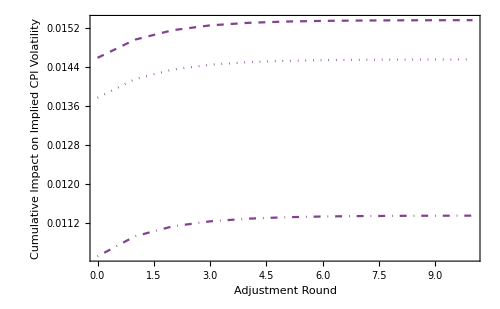

```mathematica
g1=Show[ListPlot[Table[{k,Total[rtrcoresector["L68"][[All,k+5]]]},{k,0,10}],Frame->True,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->12],AxesOrigin->{0,0},Joined->True,PlotStyle->{Dashed,RGBColor[131/255,65/255,144/255]}],ListPlot[Table[{k,Total[rtrperisector["L68"][[All,k+5]]]},{k,0,10}],Frame->True,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->12],Joined->True,PlotStyle->{DotDashed,RGBColor[131/255,65/255,144/255]}],ListPlot[Table[{k,Total[rtreusector["L68"][[All,k+5]]]},{k,0,10}],Frame->True,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->12],Joined->True,PlotStyle->{Dotted,RGBColor[131/255,65/255,144/255]}],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->12],FrameLabel->{"Adjustment Round","Cumulative Impact on Implied CPI Volatility"},PlotRange->All,ImageSize->500]
```

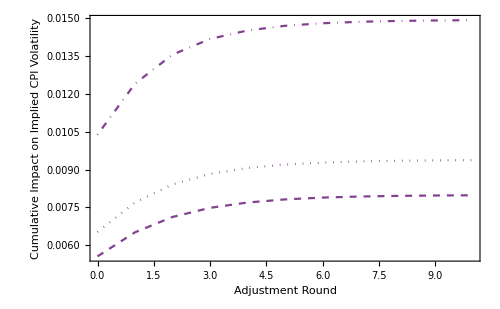

```mathematica
g2=Show[ListPlot[Table[{k,Total[rtrcoresector["C19"][[All,k+5]]]},{k,0,10}],Frame->True,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->12],PlotLegends->{"Core",Automatic},AxesOrigin->{0,0},Joined->True,PlotStyle->{Dashed,RGBColor[131/255,65/255,144/255]}],ListPlot[Table[{k,Total[rtrperisector["C19"][[All,k+5]]]},{k,0,10}],Frame->True,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->12],PlotLegends->{"Periphery",Automatic},Joined->True,PlotStyle->{DotDashed,RGBColor[131/255,65/255,144/255]}],ListPlot[Table[{k,Total[rtreusector["C19"][[All,k+5]]]},{k,0,10}],Frame->True,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->12],PlotLegends->{"EU28",Automatic},Joined->True,PlotStyle->{Dotted,RGBColor[131/255,65/255,144/255]}],LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->12],FrameLabel->{"Adjustment Round","Cumulative Impact on Implied CPI Volatility"},PlotRange->All,ImageSize->500]
```

```mathematica
Export["rtr.pdf",Grid[{{g1,Spacer[.01],g2},{"",Style["Number of Approximation Rounds",Directive[FontFamily->"Arial",Black,FontSize->12]],""}},Alignment->Bottom]]
```

rtr.pdf

```mathematica
Export["impacttableperipherydemandwpshocks.xlsx",Reverse[SortBy[Table[{Drop[prices,1][[k,1]],Drop[prices,1][[k,4]],Drop[prices,1][[k,3]],directperiphery[k],indirectperiphery[k],directperiphery[k]+indirectperiphery[k],priceshocks[[k]]},{k,1,Length[priceshocks]}],Last]]]
```

impacttableperipherydemandwpshocks.xlsx

```mathematica
Export["impacttablecoredemandwpshocks.xlsx",Reverse[SortBy[Table[{Drop[prices,1][[k,1]],Drop[prices,1][[k,4]],Drop[prices,1][[k,3]],directcore[k],indirectcore[k],directcore[k]+indirectcore[k],priceshocks[[k]]},{k,1,Length[priceshocks]}],Last]]]
```

impacttablecoredemandwpshocks.xlsx

```mathematica
Export["impacttableeudemandwpshocks.xlsx",Reverse[SortBy[Table[{Drop[prices,1][[k,1]],Drop[prices,1][[k,4]],Drop[prices,1][[k,3]],directeu[k],indirecteu[k],directeu[k]+indirecteu[k],priceshocks[[k]]},{k,1,Length[priceshocks]}],Last]]]
```

impacttableeudemandwpshocks.xlsx

```mathematica
corecorr=Transpose[{Import["impacttablecoredemandwpshocks.xlsx"][[1]][[All,-1]],Import["impacttablecoredemandwpshocks.xlsx"][[1]][[All,-2]]}];
```

```mathematica
Correlation[corecorr]
```

{{1.,0.138},{0.138,1.}}

```mathematica
pericorr=Transpose[{Import["impacttableperipherydemandwpshocks.xlsx"][[1]][[All,-1]],Import["impacttableperipherydemandwpshocks.xlsx"][[1]][[All,-2]]}];
```

```mathematica
Correlation[pericorr]
```

{{1.,0.299587},{0.299587,1.}}

```mathematica
eucorr=Transpose[{Import["impacttableeudemandwpshocks.xlsx"][[1]][[All,-1]],Import["impacttableeudemandwpshocks.xlsx"][[1]][[All,-2]]}];
```

```mathematica
Correlation[eucorr]
```

{{1.,0.20825},{0.20825,1.}}